### Mathematica Hw 5

Claus Ernst/Uta Ziegler								Math/Cs 371 Spring 2015
Due: Wednesday, March 18 before class.

Submission instructions:
Your HW 5 is to be turned in electronically. Submit one file containing all your work, the required executions, and the required explanations. Make sure your code follows standard quality expectations including (but not limited to) using meaningful variable names, using proper indentations, containing sufficient comments, using specified names and parameters and being correct.
The file name should contain the last names of the students turning it in and no spaces. E.g. ErnstZieglerHW5.nb. Your file - on the first page - must also contain the names of the students turning it in.

Additional instructions:
Use a different partner for HW 5 than you had for HW4.

#### Problem 1: Pascal’s Triangle - sideways and in colors

Pascal’s triangle is a triangle of numbers, whose tip is the number 1. Each successive row in the triangle starts with a 1 and ends with a 1, and the remaining numbers are created by adding up the two numbers in the row above to the left and right of it.
Below is a picture of the first 7 lines of Pascal’s triangle.

1

1     1

1     2     1

1     3     3     1

1     4     6     4     1

1     5     10    10    5     1

1     6     15    20    15    6     1

We want to consider the triangle rotated by a quarter turn counterclockwise. Below is a picture of the first 5 lines (= columns) of Pascal's triangle. This is not the usual way to arrange the triangle, but has the advantage that we not have to worry about the width of the screen for the rows which will start to wrap around and make the picture weird. This will allow us to look at large triangles. The original Pascal’s triangle (see above) has lines. In the rotated version we use the term column instead. Note that individual columns are vertically aligned - even if some numbers in the column contain more digits (see the colored example below).

```mathematica
uPascalsTriange[5]
```

1
 
  |  
1
1
  |  
1
2
1
  | 1
3
3
1 | 1
4
6
4
1

Do not repeat unnecessary code when writing the functions below. Call the appropriate functions instead of copying code.

a) Write a function uPascalsLine [ number ] which generates and returns a list of the elements in the given line number.
For example  uPascalsLine [ 3 ]  returns {1,2,1}.

b) Write a function uPascalsLines [ number ] which returns a list containing the first number lines of the triangle - each line being a line created by uPascalsLine. For example uPascalsLines [ 4 ] returns {{1},{1,1},{1,2,1},{1,3,3,1}}

c) Write a function uPascalsTriangle [ number ] which prints  out the first number columns of the triangle - arranged such that they form a rotated triangle as shown above. There are various Mathematica functions which control where things are displayed, such as Row, Column, TableForm and more which might be helpful here. Our solutions do not use a single Print statement.

d) Write a function uColorPascalsTriangle [ number, n ], which prints out the first number columns of the triangle like in c, except this time the values are colored as follows:
The color of a value is determined by the remainder of dividing the value by n. All values with the same remainder use the same color.
For example if n=4 then there are 4 colors, and the reminders are zero, one, two or three.
Note 1: There is no limit on the n. Your colors do not have to be the exact same colors as below, they just have to be different. 
Note 2:  In order to do this you need a colored list of values. You can either get this list by implementing ‘colored’ versions of uPascalsLine [ number, n] and uPascalsLines [number, n], or you can use the result of uPascalsLines and color it. Once you have the colored values, you proceed as in the uPascalsTriangle function

```mathematica
uColorPascalsTriangle[15,4]
```

1
 
 
 
 
 
 
  |  
 
 
 
 
 
1
1
 
 
 
 
 
  |  
 
 
 
 
 
1
2
1
 
 
 
 
 
  |  
 
 
 
 
1
3
3
1
 
 
 
 
  |  
 
 
 
 
1
4
6
4
1
 
 
 
 
  |  
 
 
 
1
5
10
10
5
1
 
 
 
  |  
 
 
 
1
6
15
20
15
6
1
 
 
 
  |  
 
 
1
7
21
35
35
21
7
1
 
 
  |  
 
 
1
8
28
56
70
56
28
8
1
 
 
  |  
 
1
9
36
84
126
126
84
36
9
1
 
  |  
 
1
10
45
120
210
252
210
120
45
10
1
 
  |  
1
11
55
165
330
462
462
330
165
55
11
1
  |  
1
12
66
220
495
792
924
792
495
220
66
12
1
  | 1
13
78
286
715
1287
1716
1716
1287
715
286
78
13
1 | 1
14
91
364
1001
2002
3003
3432
3003
2002
1001
364
91
14
1

e) The colorings of the values form patterns, however they are hard to see because the values become larger and larger and take more and more space. To see the patterns better let us remove the numbers and replace them with a dot.
Write a function uColorPascalsTriangleDot [ number, n ], which displays the first number columns however we only see a “dot” instead of each value. The color of each dot is determined in the same manner as the color of each value in d).
Note 3:  In order to do this you need a colored list of dots. You can either get this list by implementing ‘colored dotted’ versions of uPascalsLine [ number, n] and uPascalsLines [number, n], or you can use the result of uPascalsLines and ‘color dot’ it. Once you have the colored dots, you proceed as in the uPascalsTriangle function.
Note 4:  ● is a special character in Mathematica, and you can display it with different colors. There is a palette with special characters. Select Palettes -> Special Characters.


The example in d) looks now like this:

```mathematica
uColorPascalsTriangleDot[15,4]
```

●
 
 
 
 
 
 
  |  
 
 
 
 
 
●
●
 
 
 
 
 
  |  
 
 
 
 
 
●
●
●
 
 
 
 
 
  |  
 
 
 
 
●
●
●
●
 
 
 
 
  |  
 
 
 
 
●
●
●
●
●
 
 
 
 
  |  
 
 
 
●
●
●
●
●
●
 
 
 
  |  
 
 
 
●
●
●
●
●
●
●
 
 
 
  |  
 
 
●
●
●
●
●
●
●
●
 
 
  |  
 
 
●
●
●
●
●
●
●
●
●
 
 
  |  
 
●
●
●
●
●
●
●
●
●
●
 
  |  
 
●
●
●
●
●
●
●
●
●
●
●
 
  |  
●
●
●
●
●
●
●
●
●
●
●
●
  |  
●
●
●
●
●
●
●
●
●
●
●
●
●
  | ●
●
●
●
●
●
●
●
●
●
●
●
●
● | ●
●
●
●
●
●
●
●
●
●
●
●
●
●
●

f) Investigate the patterns you find when your run uColorPascalsTriangleDot [ number, n ] for n=2,3,4,....
Describe some of the patterns you see for or small numbers of n.

#### Problem 2: Catch me if you can with escape door.

This is a modified version of the problem we discussed in class during the last week. This problem is designed to use the same type of simulation using small line segments as steps that we discussed in class.

The problem: For simplicity we assume that you are in a very large circular room - think of Diddle arena.
No obstacles are in the room - but there is one door on the “north pole of the circle.
There are two people: the runner with speed v2 and the catcher with speed v1. The runner wins if the runner reaches the door before she/he is caught. The runner is caught if the catcher comes with distance rad/50 of the runner.
Any program you write for this problem should return a graphic like the one below with the runner in red and the catcher in blue and the door as a black dot on the top. The graphic shows the paths each person walks; the small dot is the starting position and the bigger dot is the current position. In the graphic below the runner is faster (its path is longer) and the runner can now head straight towards the door to win. 
Note that this is not a graphic that will be generated by the code in problem 2, it is just a graphic that illustrates how this could look like.

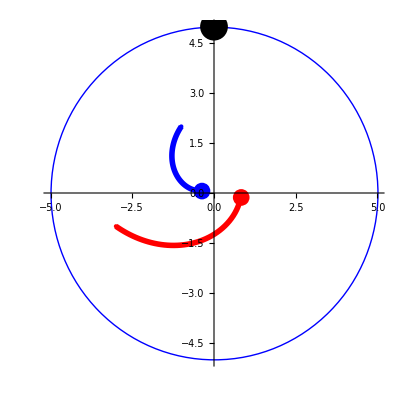

The description below uses the following notation:
{cx,cy} = the starting position of the catcher and v1 is the speed of the catcher.
{rx,ry} = the starting position of the runner and v2 is the speed of the runner.
The circle has the origin as the center and radius rad and the door is at {0,rad}. 
timestep determines the length of the line segment for each step.
The catcher uses v1* timestep as the length of one step and the runner uses v2* timestep as the length of one step. 
n is the number of steps in the simulation.

a) Write a function uCatchmeDoorSleep [ {cx,cy}, {rx,ry}, v1, v2, timestep, rad, n ], where the catcher is asleep (not moving) and the runner runs in a straight line towards the door with the correct step length as explained above. The runner should stop once the door is reached, i.e. the runner should not move past the point (0,rad) - even if the number of steps n is larger than what is needed to reach the door. The runner just stops at the door and does not move anymore.

b) Assume that the runner moves as implemented in part a). Discuss a strategy that the catcher can use to intercept the runner and explain how you know that this is  a good strategy.

c) Implement the strategy for the catcher that you describe in part b) by creating the function below

```mathematica
uCatchmeDoor[{cx,cy},{rx,ry},v1,v2,timestep,rad,n]
```

Again the output will be graphic. The runner and catcher should stop moving if either the runner reaches the door or the catcher caught the runner, i.e is within distance or rad/50 of the runner.

d) Use the Manipulate command to illustrate how your strategy will work out in a variety of cases.

Your test cases must include the following:

(i) {cx,cy}= {-2,-3},{rx,ry}={1,-2},v1=1,v2=1,timestep=.1,rad=5
(ii) {cx,cy}= {-2,-3},{rx,ry}={1,-3},v1=1,v2=1,timestep=.1,rad=5
(iii) {cx,cy}= {-2,3},{rx,ry}={1,-3},v1=1,v2=2,timestep=.1,rad=5
(iv) {cx,cy}= {-2,3},{rx,ry}={1,3},v1=2,v2=1,timestep=.1,rad=5

e) Extra credit: Any additonal strategy that you can add in the code for the runner will give you some extra credit. Call the function you create

```mathematica
uCatchmeDoorExtra[{cx,cy},{rx,ry},v1,v2,timestep,rad,n]
```

You need to clearly explain the strategy you added and show by examples that it works.